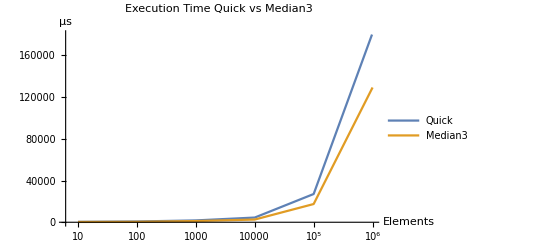

```mathematica
quick = {{10, 368},{100, 726},{1000, 1758},{10000, 4505},{100000, 27079},{1000000, 181452}};
median3 = {{10, 281},{100, 417},{1000, 1127},{10000, 2602},{100000, 17475},{1000000, 129227}};
ListLogLinearPlot[{quick, median3}, AxesLabel->{"Elements", "µs"}, Joined->True, PlotLabel->"Execution Time Quick vs Median3", PlotLegends->{"Quick", "Median3"}, PlotRange->{0, 180000}]
```